# 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{n,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"M","y"},BaseStyle->{FontSize->20}]
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0}(*{(*maxran-20*)20,limit+.05}*),{(*maxran-25*)(*15*)ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos(*{(*maxran-20*)22,limit+.05}*),Left]},{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]},Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" },
{{funplot,DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]},{0,1},ControlType->None},
{{ilimpos,If[limpos===Automatic,{22,limit+05},limpos]},ControlType->None},
SaveDefinitions->True,Initialization:>{epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}]}
]
]
```

# 1) Arctan

arctan(x)=∑_(n=0)^∞ (-1)^n x^(2n+1)/(2n+1)  ?

x∈(-1,1)

#### Useful formulas

Ableitung of the inverse function (Satz 11.4)

(f^-1)'(y)=1/(f'(x)), where y=f(x)

Integration of Funktionenfolgen (Satz 15.1)

f_n Folge, stetige Funktionen, gleichmäßig konvergiert  gegen f  ⇒   lim_(n→∞) ∫_a^b f_n(x)ⅆx=∫_a^b f(x)ⅆx

## Solution

First, we calculate arctan'(y) using Satz 11.4:

arctan'(y)=1/(tan'(x)) with y=tan(x)

We also know that tan'(x)=1/(cos^2(x)) and so:

arctan'(y)=cos^2(x)

But we want to express the Ableitung of arctan with the help of y, not x. We note that:

tan^2(x)=((sin(x))/(cos(x)))^2=(1-cos^2(x))/(cos^2(x))=1/(cos^2(x))-1

where in the second equality we used identity sin^2(x)+cos^2(x)=1. From the last equality we get:

cos^2(x)=1/(1+tan^2(x))=1/(1+y^2)

That is: arctan'(y)=1/(1+y^2)=1/(1-(-y^2)).

We also know that the geometric series evaluates to:

∑_(k=0)^∞ q^k=1/(1-q) for Abs[g]<1

When we set q:=-y^2, we obtain:

arctan'(y)=∑_(k=0)^∞ (-y^2)^k=∑_(k=0)^∞ (-1)^k y^(2k)

As we investigate only those values of y for which Abs[y]<1 (follows from the Angabe), the Reihe above converges: Abs[q]=Abs[-y^2]=Abs[y]^2<1.

Strictly speaking, Reihe ∑_(k=0)^∞ (-1)^k y^(2k) is a limit of Funktionenfolge f_n(y)=∑_(k=0)^n (-1)^k y^(2k). From Satz 10.12. we know that Funktionenfolge ∑_(k=0)^n q^k converges gleichmäßig on interval (-1,1) towards ∑_(k=0)^∞ q^k.

Assumptions of Satz 15.1 are therefore satisfied and we can integrate both sides of equality arctan'(y)=∑_(k=0)^∞ (-1)^k y^(2k)=lim_(n→∞) f_n(y) to get:

lim_(n→∞) ∫_0^x f_n(y)ⅆy=∫_0^x arctan'(y)ⅆy

The right-hand side equals arctan(x) and the left-hand side is equal to:

lim_(n→∞) ∫_0^x f_n(y)ⅆy=lim_(n→∞) ∫_0^x ∑_(k=0)^n (-1)^k y^(2k)ⅆy=lim_(n→∞) ∑_(k=0)^n (-1)^k x^(2k+1)/(2k+1)=∑_(k=0)^∞ (-1)^k x^(2k+1)/(2k+1)

Putting everything together we obtain:

arctan(x)=∑_(k=0)^∞ (-1)^k x^(2k+1)/(2k+1)

# 2) Extremstellen

a) f: ℝ→ℝ;  n∈ℕ

f(x)=x^-n ⅇ^x

b) f:ℝ_+→ℝ

f(x)=x-ln(x^2)

c) f:ℝ_+→ℝ;   a_1, a_2>0

f(r)=a_1/r^12-a_2/r^6

#### Useful formulas

Extremum vs. Ableitung (Satz 11.11)

f has Extremum in x_0   ⇒   f'(x_0)=0

Minimum, Maximum vs. Ableitung (Satz 11.17)

f''(x_0)>0   ⇒   f has a local Minimum in x_0
f''(x_0)<0   ⇒   f has a local Maximum in x_0

Ableitung of a composite function (Satz 11.3)

(g ◦ f)'(x)=g'(f(x))·f'(x)

## Plots

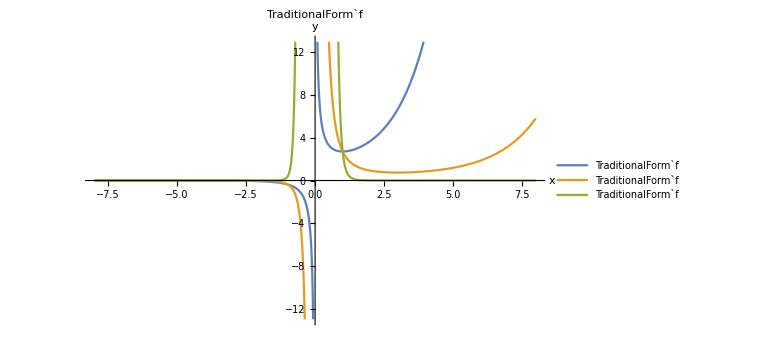

```mathematica
plotFun[{x^-1 ⅇ^x,x^-3 ⅇ^x,x^-10 ⅇ^x},{{-8,8},{-13,13}},{},"TraditionalForm`f",{"TraditionalForm`f","TraditionalForm`f","TraditionalForm`f"}]
```

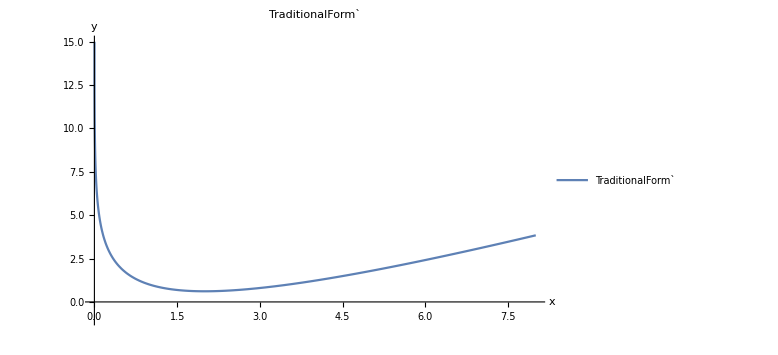

```mathematica
plotFun[{x-Log[x^2]},{{0,8},{-1,15}},{},"TraditionalForm`",{"TraditionalForm`"}]
```

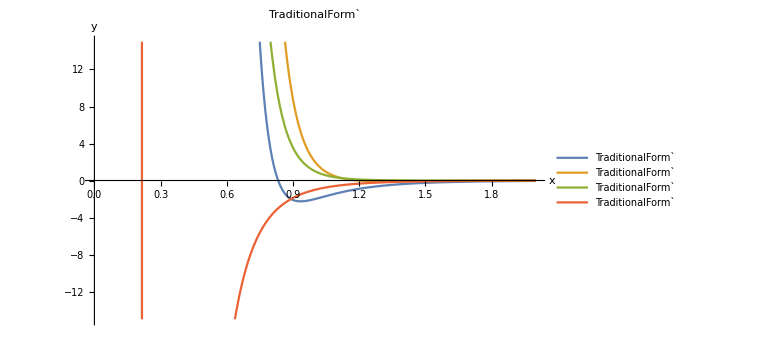

```mathematica
plotFun[{With[{a1=1,a2=3},a1/x^12-a2/x^6],With[{a1=3,a2=1},a1/x^12-a2/x^6],With[{a1=1,a2=0.0001},a1/x^12-a2/x^6],With[{a1=0.0001,a2=1},a1/x^12-a2/x^6]},{{0,2},{-15,15}},{},"TraditionalForm`",{"TraditionalForm`","TraditionalForm`","TraditionalForm`","TraditionalForm`"}]
```

## Solution

## a)

To determine all local Extremstellen, we need to calculate the first and second Ableitung of function f:

f'(x)=(x^-n ⅇ^x)'=-n x^(-(n+1))ⅇ^x+ x^-n ⅇ^x=ⅇ^x/x^n(1-n/x)=f(x)(1-n/x)

f''(x)=(f(x)(1-n/x))'=f'(x)(1-n/x)+f(x)(n/x^2)=f(x)(1-n/x)^2+f(x)(n/x^2)

Extremstellen satisfy f'(x)=0, which is in our case:

f(x)(1-n/x)=0

As f(x) is never zero, we get one Extremstelle at x=n, for which 1-n/x=0.

To determine whether this Extremstelle is a minimum or maximum, we check whether the second Ableitung at x=n is positive or negative:

f''(x)|_(x=n)=f(x)(1-n/x)^2|_(x=n)+ f(x)(n/x^2)|_(x=n)=1/n f(n)=1/n·ⅇ^n/n^n>0

The second Ableting is positive for any n∈ℕ and we conclude that the Extremstelle is a local 
minimum.

What about global extrema?

As lim_(x→∞) f(x)=lim_(x→∞) x^-n ⅇ^x=∞ and lim_(x↘0) f(x)=lim_(x↘0) x^-n ⅇ^x=∞ there is no global maximum.

For gerade n one gets: lim_(x↗0) f(x)=lim_(x↗0) x^-n ⅇ^x=∞ and lim_(x→-∞) f(x)=lim_(x→-∞) x^-n ⅇ^x=0. Could there be a global minimum equal to zero? No, because there is no x∈ℝ for which f(x)=0. There is therefore no global minimum for gerade n.

For ungerade n one gets: lim_(x↗0) f(x)=lim_(x↗0) x^-n ⅇ^x=-∞. There is therefore no global minimum for ungerade n.

See below plots of function f for three specific examples of n with Extremstellen x=n marked by dashed lines:

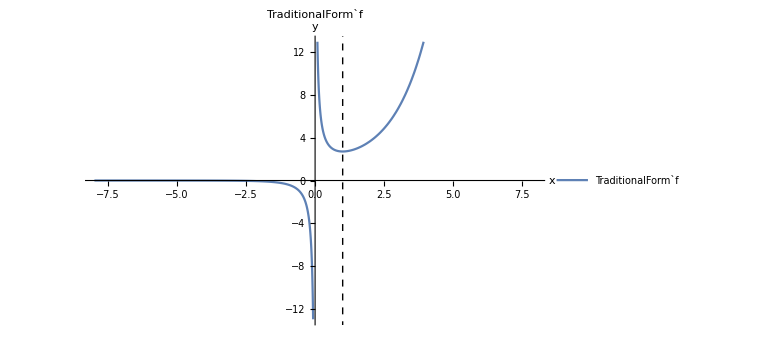

```mathematica
plotFun[{x^-1 ⅇ^x},{{-8,8},{-13,13}},{Dashed,InfiniteLine[{1,0},{0,1}]},"TraditionalForm`f",{"TraditionalForm`f"}]
```

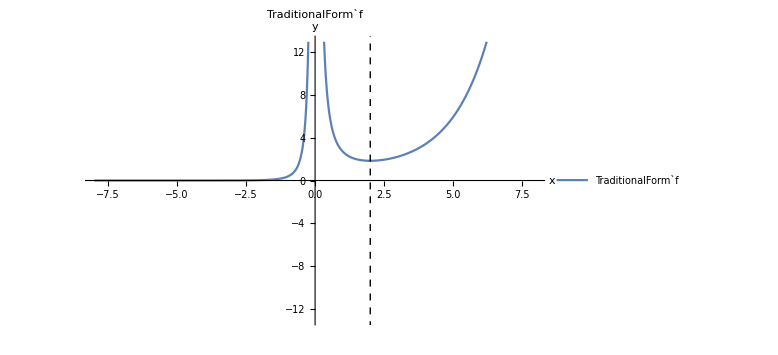

```mathematica
plotFun[{x^-2 ⅇ^x},{{-8,8},{-13,13}},{Dashed,InfiniteLine[{2,0},{0,1}]},"TraditionalForm`f",{"TraditionalForm`f"}]
```

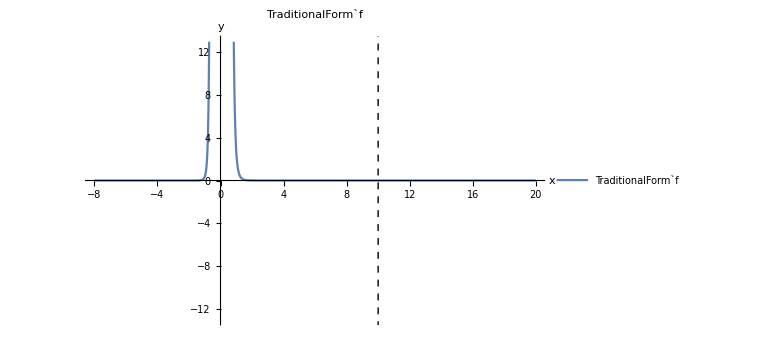

```mathematica
plotFun[{x^-10 ⅇ^x},{{-8,20},{-13,13}},{Dashed,InfiniteLine[{10,0},{0,1}]},"TraditionalForm`f",{"TraditionalForm`f"}]
```

## b)

For details see a).

f'(x)=(x-ln(x^2))'=(x-2ln(x))'=1-2/x

We get f'(x)=0 for x=2. At this point the second Ableitung is positive as:

f''(x)|_(x=2)=(1-2/x)'|_(x=2)=2/x^2|_(x=2)=2/4=1/2>0

Thence, for x=2 function f has a local minimum.

As for the global extrema, there is no global maximum as lim_(x→∞) f(x)=lim_(x→∞) (x-ln(x^2))=∞ and lim_(x→0) f(x)=lim_(x→0) (x-ln(x^2)=∞. Nonetheless, the local minimum is also a global minimum at x=2.

See below a plot of function f with the Extremstelle x=2 marked by a dashed line:

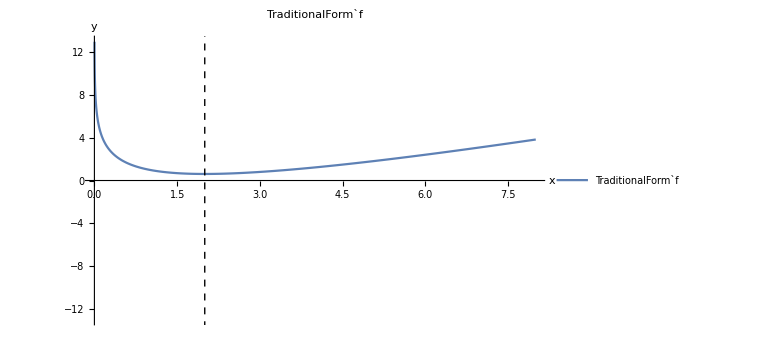

```mathematica
plotFun[{x-ln(x^2)},{{0,8},{-13,13}},{Dashed,InfiniteLine[{2,0},{0,1}]},"TraditionalForm`f",{"TraditionalForm`f"}]
```

## c)

For details see a).

f'(r)=(a_1/r^12-a_2/r^6)'=a_1-12/r^13-a_2-6/r^7=6/r^7(a_1-2/r^6+a_2)

We get f'(r)=0 for a_2=a_1 2/r^6, i.e. for r=((2 a_1)/a_2)^(1/6). At this point the second Ableitung is positive as (a_1,a_2>0):

f''(r)|_(r=((2 a_1)/a_2)^(1/6))=(6/r^7(a_1-2/r^6+a_2))'|_(r=((2 a_1)/a_2)^(1/6))=…=(6/r^8((26 a_1)/r^6-7 a_2))|_(r=((2 a_1)/a_2)^(1/6))=6/((((2 a_1)/a_2)^(1/6))^8)(13 a_2-7 a_2)=(36 a_2)/((((2 a_1)/a_2)^(1/6))^8)>0

For r=((2 a_1)/a_2)^(1/6)  therefore function f has a local minimum. Its value is equal to f(((2 a_1)/a_2)^(1/6))=a_1/((2 a_1)/a_2)^2-a_2/((2 a_1)/a_2)=-a_2^2/(4 a_1).

As for the global extrema, we have lim_(r→0) f(r)=lim_(r→0) (a_1/r^12-a_2/r^6)=lim_(r→0) ((a_1-a_2 r^6)/r^12)=lim_(r→0) (1/r^12)·a_1=∞.

There is therefore no global maximum. We also have lim_(r→∞) f(r)=lim_(r→∞) (a_1/r^12-a_2/r^6)=0. As this value (zero) is larger than the local minimum -a_2^2/(4 a_1) (which is negative), we conclude that the local minimum is actually the global minimum.

See below plots of function f with the Extremstelle r=((2 a_1)/a_2)^(1/6) marked by a dashed line:

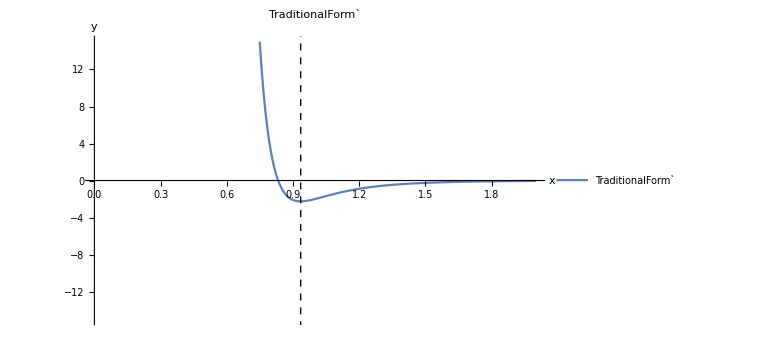

```mathematica
With[{a1=1,a2=3},plotFun[{a1/x^12-a2/x^6},{{0,2},{-15,15}},{Dashed,InfiniteLine[{((2 a1)/a2)^(1/6),0},{0,1}]},"TraditionalForm`",{"TraditionalForm`"}]]
```

# 3) Ungleichung

(ln(x)+ln(y))/2≤ln((x+y)/2) ?

x,y>0

#### Useful formulas

Konkave Funktion (Definition 11.6)

f konkav ⇔  f(λ x +(1-λ)y)≥λ f(x)+(1-λ)f(y)

Konkave Funktion (Satz 11.18)

f konkav ⇔ f''≤0

## Solution

Let us define f(x):=ln(x) and use Satz 11.18:

f'(x)=1/x

f''(x)=-1/x^2<0 ⇒ f is konkav

Since f is konkav, it follows (when we choose λ=1/2) from the Definition 11.6 that:

f(x/2 +(1-1/2)y)≥1/2 f(x)+(1-1/2)f(y)

After simplification of this inequality we obtain:

ln((x+y)/2)≥(ln(x)+ln(y))/2

as we wanted to show.

# 4) Potentielle Energie

Ortsabhängige Kraft F, potentielle Energie V:
F=-V'
V=?

a) Harmonische Kraft
     F(x)=-k x      k>0, x∈ℝ

b) Newtonsche Gravitationskraft
     F(r)=-(G M m)/r^2      G,M,m,r>0

c) Lennard-Jones Kraft
     F(r)=(-C_1/r)^13+(C_2/r)^7     C_1, C_2>0

## Solution

## a)

Since V'(x)=-F(x)=-(-k x)=k x, we get:

V(x)=∫(-F(x))ⅆx=∫k x ⅆx=k∫x ⅆx=k x^2/2+C

for some constant C. That is:

V(x)=k x^2/2+C

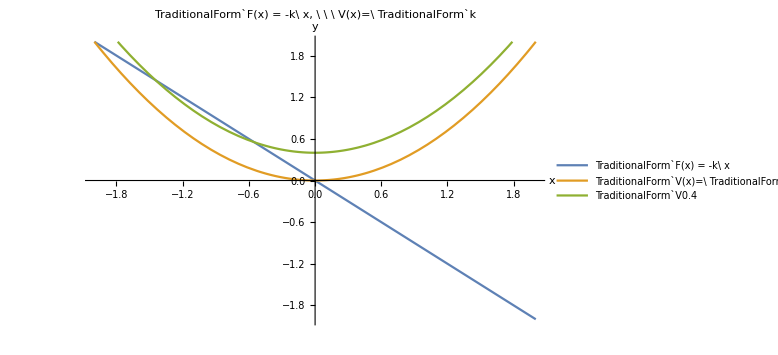

```mathematica
With[{k=1,c=0,c2=.4},plotFun[{-k x,k x^2/2+c,k x^2/2+c2},{{-2,2},{-2,2}},{},"TraditionalForm`F(x) = -k\ x, \ \ \ V(x)=\ TraditionalForm`k",{"TraditionalForm`F(x) = -k\ x","TraditionalForm`V(x)=\ TraditionalForm`k","TraditionalForm`V0.4"}]]
```

## b)

Since V'(r)=-F(r)=-(-(G M m)/r^2)=(G M m)/r^2, we get:

V(r)=∫(-F(r))ⅆr=∫(G M m)/r^2 ⅆr=G M m∫r^-2 ⅆr=G M m-1/r+C

for some constant C. That is:

V(r)=-(G M m)/r+C

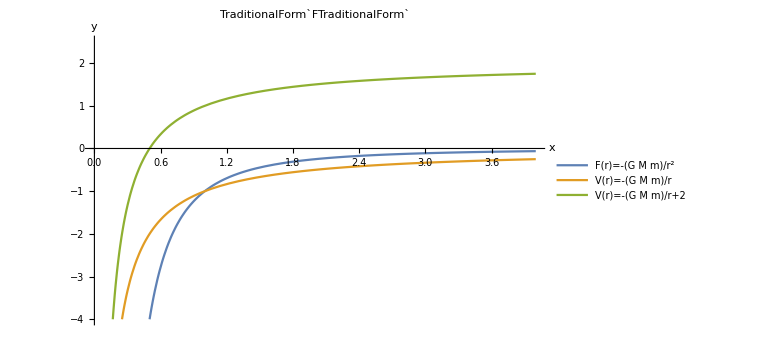

```mathematica
With[{k=1,c=0,c2=2},plotFun[{-k/x^2,-k/x+c,-k/x+c2},{{0,4},{-4,2.5}},{},"TraditionalForm`FTraditionalForm`",{"F(r)=-(G M m)/r^2","V(r)=-(G M m)/r","V(r)=-(G M m)/r+2"}]]
```

## c)

Since V'(r)=-F(r)=-((-C_1/r)^13+(C_2/r)^7)=(C_1/r)^13-(C_2/r)^7, we get:

V(r)=∫(-F(r))ⅆr=∫(C_1^13 r^-13-C_2^7 r^-7) ⅆr=C_1^13∫r^-13 ⅆr-C_2^7∫r^-7 ⅆr=C_1^13(r^-12/-12)-C_2^7(r^-6/-6)+C

for some constant C. That is:

V(r)=(-C_1^13/12)1/r^12+(C_2^7/6)1/r^6+C

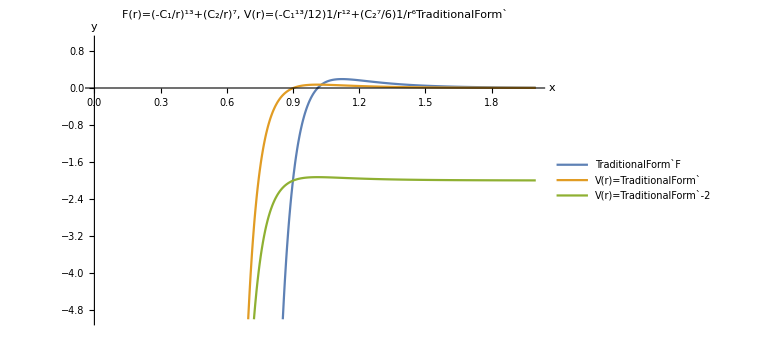

```mathematica
With[{k=1,cc1=1,cc2=.99,c=0,c2=-2},plotFun[{(-cc1/x)^13+(cc2/x)^7,(-cc1^13/12)1/x^12+(cc2^7/6)1/x^6+c,(-cc1^13/12)1/x^12+(cc2^7/6)1/x^6+c2},{{0,2},{-5,1}},{},"F(r)=(-C_1/r)^13+(C_2/r)^7, V(r)=(-C_1^13/12)1/r^12+(C_2^7/6)1/r^6TraditionalForm`",{"TraditionalForm`F","V(r)=TraditionalForm`","V(r)=TraditionalForm`-2"}]]
```

# 5) Stammfunktionen

a) ∫ⅆx/(√(a^2-x^2))=arcsin(x/a),   a>Abs[x]

b) ∫ⅆx/(√(a^2+x^2))=arsinh(x/a),   a>0

c) ∫sinh^2(x)ⅆx=1/4 sinh(2x)-1/2 x

d) ∫cos^2(x)ⅆx=1/4 sin(2x)+1/2 x

#### Useful formulas

Stammfunktion (Definition 11.8)

F Stammfunktion von f  ⇔  F'=f

Ableitung of a composite function (Satz 11.3)

(g ◦ f)'(x)=g'(f(x))·f'(x)

Ableitung of the inverse function (Satz 11.4)

(f^-1)'(y)=1/(f'(x)), where y=f(x)

## Solution

## a)

Function arcsin(x/a) is the Stammfunktion of 1/(√(a^2-x^2)), when (arcsin(x/a))'=1/(√(a^2-x^2)). So we have to prove this equation

We start by calculating the Ableitung of arcsin alone using Satz 11.4:

arcsin'(y)=1/(sin'(x))=1/(cos(x)) with y=sin(x)

We would like to express the Ableitung of arcsin with the help of x, not y. To that end we use identity sin^2(x)+(cos(x))^2=1, from where:

cos(x)=√(1-sin^2(x))=√(1-y^2)

That is:

arcsin'(y)=1/(√(1-y^2))

When we use y=x/a, we obtain:

arcsin'(x/a)=1/(√(1-(x/a)^2))=a/(√(a^2-x^2)),
where we assume a>0 (follows from a>Abs[x] given in the Angabe).

(Function arcsin is defined only for values y∈(-1,1), that is only when Abs[x/a]<1. This is satisfied whenever Abs[x]<a.)

For the Ableitung of a composite function arcsin(x/a) we therefore get:

(arcsin(x/a))'=arcsin'(x/a)·1/a=1/a·a/(√(a^2-x^2))=1/(√(a^2-x^2))
as we wanted to show.

## b)

Similarly to a), we want to show (arsinh(x/a))'=1/(√(a^2+x^2)), where a>0. Similarly to a) we can use Satz 11.4 and identity cosh^2(x)-sinh^2(x)=1 to show:

arsinh'(y)=1/(√(1+y^2))

When we make a substitution y=x/a we get:

(arsinh(x/a))'=1/a·arsinh'(x/a)=1/a·a/(√(a^2+x^2))=1/(√(a^2+x^2))

as was to be done.

## c)

For details see a).

(1/4 sinh(2x)-1/2 x)'=1/4 cosh(2x)2-1/2=1/2(cosh(2x)-1)

Also:

cosh(2x)=1/2(ⅇ^(2x)+ⅇ^(-2x))=1/2((ⅇ^x)^2+(ⅇ^-x)^2-2+2)=2((ⅇ^x-ⅇ^-x)/2)^2+1=2sinh^2(x)+1

Therefore:

(1/4 sinh(2x)-1/2 x)'=1/2(cosh(2x)-1)=1/2((2sinh^2(x)+1)-1)=sinh^2(x)

## d)

For details see a).

(1/4 sin(2x)+1/2 x)'=1/4 cos(2x)2+1/2=1/2(cos(2x)+1)

Also:

cos(2x)=cos^2(x)-sin^2(x)=cos^2(x)-(1-cos^2(x))=2cos^2(x)-1

Therefore:

(1/4 sin(2x)+1/2 x)'=1/2(cos(2x)+1)=1/2((2cos^2(x)-1)+1)=cos^2(x)